```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
k=Flatten[Import["./k1.dat"]]/197.33;
lam1=Flatten[Import["./lam1.dat"]];
lam2=Flatten[Import["./lam2.dat"]];
lam1dl=lam1[[1;;Length[k]]]*k^-2;
lam2dl=lam2[[1;;Length[k]]]*k^-1*59.437186;
```

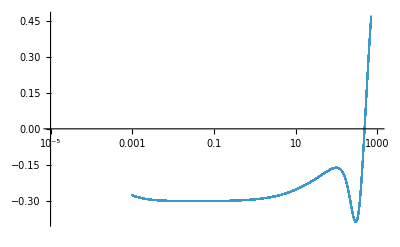

```mathematica
Show[ListPlot[Transpose[{k*197.33,lam1dl}],PlotRange->{{10^-5,1000},All},ScalingFunctions->{"Log",Automatic}]]
```

```mathematica
lam1dl[[-1]]
```

-0.277905

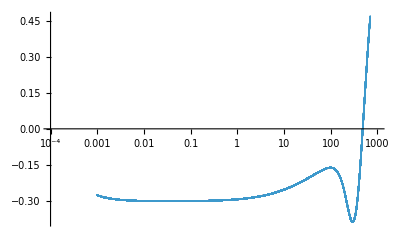

```mathematica
ListPlot[Transpose[{k*197.33,lam1dl}],PlotRange->{{10^-4,1000},All},ScalingFunctions->{"Log",Automatic}]
```

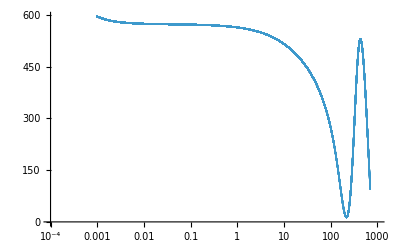

```mathematica
ListPlot[Transpose[{k*197.33,lam2dl}],PlotRange->{{10^-4,1000},All},ScalingFunctions->{"Log",Automatic}]
```